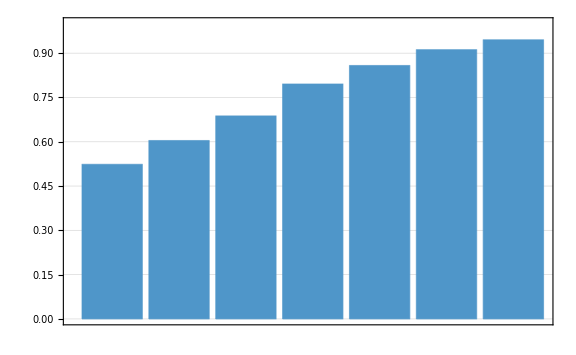

```mathematica
BarChart[{(4 π)/3,(4 π)/3+32/3 (2-Sqrt[3])^3 π,5.50012,6.36494,6.86641,7.2947,7.56267}/8,PlotRange->{0,1},ChartBaseStyle->EdgeForm[Thick],ChartStyle->ColorData[97][54],PlotTheme->{"Detailed",TicksStyle->Directive[Red]},ImageSize->Large]
```

```mathematica
Export["barplot.svg",BarChart[{(4 π)/3,(4 π)/3+32/3 (2-Sqrt[3])^3 π,5.50012,6.36494,6.86641,7.2947,7.56267}/8,PlotRange->{0,1},ChartBaseStyle->EdgeForm[Thick],ChartStyle->ColorData[97][54],PlotTheme->"Detailed",ImageSize->Large]]
```

barplot.svg

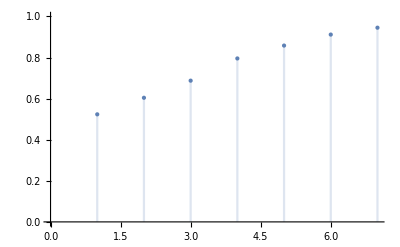

```mathematica
DiscretePlot[{(4 π)/3,(4 π)/3+32/3 (2-Sqrt[3])^3 π,5.50012,6.36494,6.86641,7.2947,7.56267}[[k]]/8,{k,1,7},PlotStyle->PointSize[Large],PlotRange->{0,1}]
```